# Simple analysis, 4/1/2018

## Mean

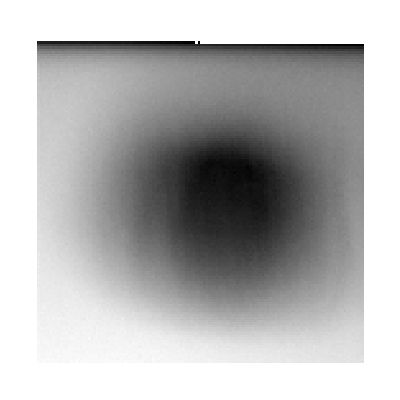

```mathematica
dataTest1 = Flatten[Import["/Volumes/kaufman_heap/heap/180329/Andor_imaging/with_atoms/img_53.fits", "RawData"],1];
numShots = Length[dataTest1];
avg1 = Total[dataTest1]/numShots;
ArrayPlot[avg1, PlotRange-> {11000,11200}]
```

```mathematica
dataTest2 = Flatten[Import["/Volumes/kaufman_heap/heap/180329/Andor_imaging/with_atoms/img_35.fits", "RawData"],1];
numShots = Length[dataTest2];
avg2= Total[dataTest2]/numShots;
ArrayPlot[avg2, PlotRange-> {11000,11200}]
```

-Graphics-

#### Difference

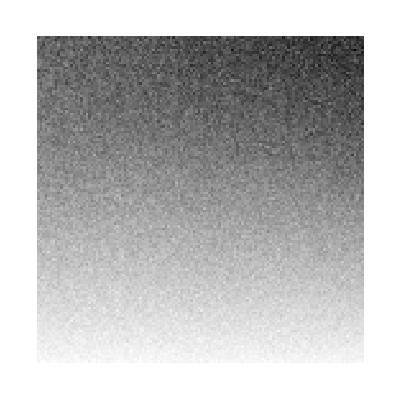

```mathematica
ArrayPlot[avg1-avg2]
```

```mathematica
128^2/4*200*1.4*20
```

2.29376×10^7

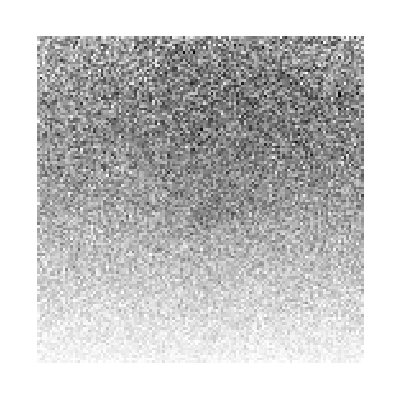

-Graphics-

## Standard deviation

```mathematica
getVariance[data_,i_,j_]:=(
dataSTD = Map[#[[i,j]]&,data];
std = StandardDeviation[dataSTD];
Return[std]
);
```

```mathematica
StandardDeviation[dataSTD]
```

32.3867

```mathematica
stdData = Table[getVariance[dataTest,i,j],{i,1,Dimensions[dataTest][[2]]},{j,1,Dimensions[dataTest][[3]]}];
```

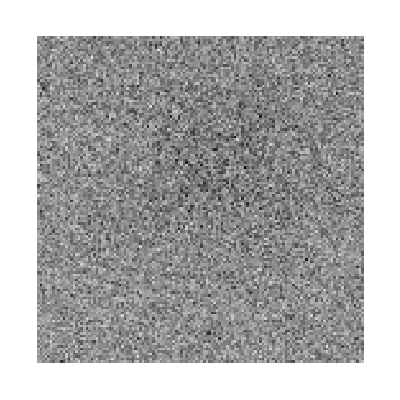

```mathematica
ArrayPlot[stdData]
```

## Bg sub, every other shot; single sequence of many repititions

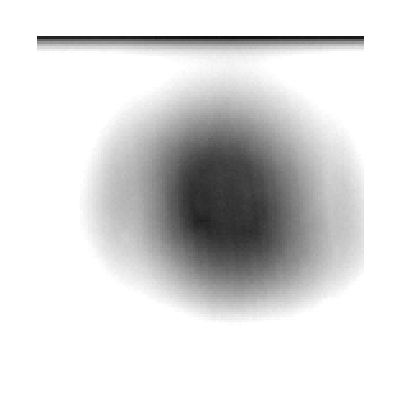

```mathematica
dataImages = Flatten[Import["/Volumes/kaufman_heap/heap/180330/img_59.fits", "RawData"],1];
numShots = Length[dataImages];
dimx = Dimensions[dataImages][[2]];
dimy = Dimensions[dataImages][[3]];
avg1 = Total[dataImages]/numShots;
ArrayPlot[avg1, PlotRange-> {11000,11200}]
```

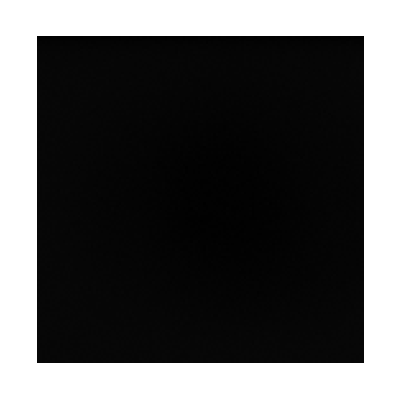

```mathematica
ArrayPlot[dataImages[[1]]]
```

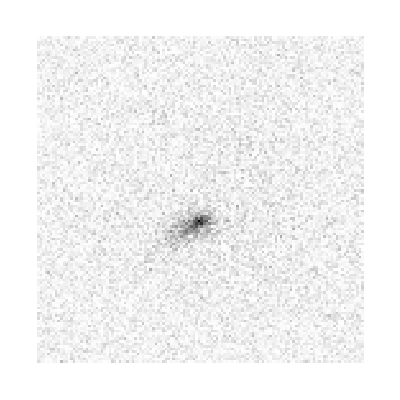

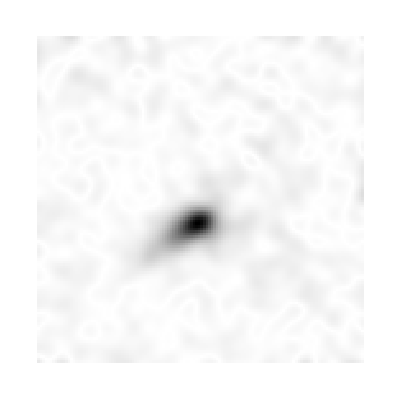

-Graphics3D-

-Graphics3D-

{{0.18,-1.2,0.43,-0.05,2.94,-2.44,-0.69,-0.85,-0.97,0.49,-2.11,-2.55,-5.64,-1.96,-0.8,-3.62,96,-2.69,-2.15,0.36,-2.35,0.19,0.47,-0.24,-0.95,2.99,1.16,1.02,-1.94,-0.12,-0.71,-1.59,3.31},126,{1}}
 |  |  |  |

```mathematica
initMat = Table[0,{i,1,dimx},{j,1,dimy}];
Do[
diffImage = dataImages[[shot]]- dataImages[[shot+1]];
initMat = initMat+diffImage;
,{shot,1,numShots,2}]
finMat = initMat/(1/2 numShots);
ArrayPlot[finMat]
ArrayPlot[LowpassFilter[finMat,.5], PlotRange-> All]
ListPlot3D[LowpassFilter[finMat,.5], PlotRange-> All]
ListPlot3D[finMat, PlotRange-> All]
finMat
```

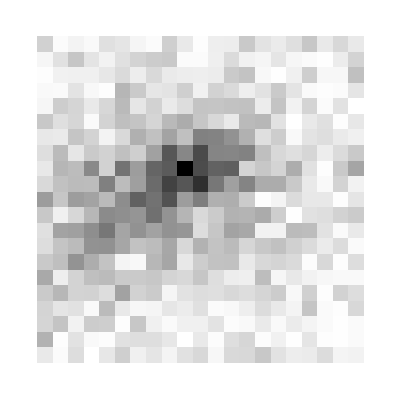

```mathematica
ArrayPlot[finMat[[65;;85,55;;75]]]
```

```mathematica
Total[Flatten[finMat[[65;;85,55;;75]]]]
```

2133.98

391.16

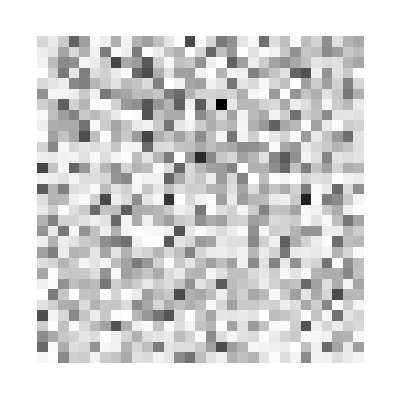

```mathematica
Total[Flatten[finMat[[85;;115,75;;105]]]]
ArrayPlot[finMat[[85;;115,75;;105]]]
```

```mathematica
1800-400
```

1400

```mathematica
1400*1.4/.05/1800
```

21.7778

```mathematica
.2*12*180
```

432.

```mathematica
180*.3
```

54.

```mathematica
.15*12*180
```

324.

```mathematica
.700/300*180/π/.02
```

6.68451

## Bg sub, every other shot, scan parameter; multiple variations, multiple reptitions

```mathematica
numVariations = 10;
initVal =1.7;
finVal =1.9;
keyFunc[index_]=initVal+(index-1)*(finVal-initVal)/numVariations;
rawKeys=Table[i,{i,1,10}]
keyVals =Subdivide[initVal,finVal, numVariations]
```

{1,2,3,4,5,6,7,8,9,10}

{1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9}

```mathematica
Subdivide[ 1.86,1.9, 10]
```

{1.86,1.864,1.868,1.872,1.876,1.88,1.884,1.888,1.892,1.896,1.9}

```mathematica
keyVals
```

{1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9}

```mathematica
Range[]
```

Range::argb: Range called with 0 arguments; between 1 and 3 arguments are expected.

Range[]

```mathematica
repititions=20;
allImages = Flatten[Import["/Volumes/kaufman_heap/heap/180402/img_135.fits", "RawData"],1];
numShots = Length[allImages];
dimx = Dimensions[allImages][[2]];
dimy = Dimensions[allImages][[3]];
avg1 = Total[allImages]/numShots;
ArrayPlot[avg1, PlotRange-> {11000,11200}]
```

-Graphics-

```mathematica
dataList = {};
arrayList = {};
Do[
dataImages = allImages[[(j-1)*2repititions+1;;j*repititions*2]];
initMat = Table[0,{i,1,dimx},{j,1,dimy}];
Do[
diffImage = dataImages[[shot]]- dataImages[[shot+1]];
initMat = initMat+diffImage;
,{shot,1,2repititions,2}];
finMat = initMat/(repititions);
AppendTo[dataList, {keyVals[[j]],Total[Flatten[finMat]] }];
AppendTo[arrayList, {keyVals[[j]],finMat}];
,{j,1,numVariations}]
```

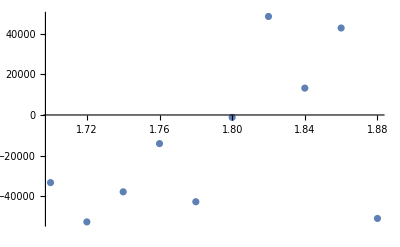

```mathematica
ListPlot[dataList]
```

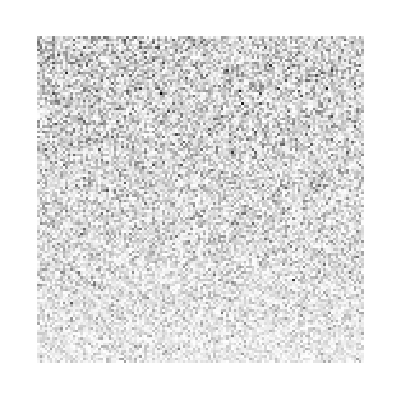
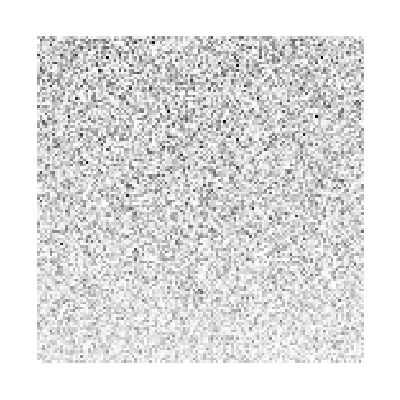
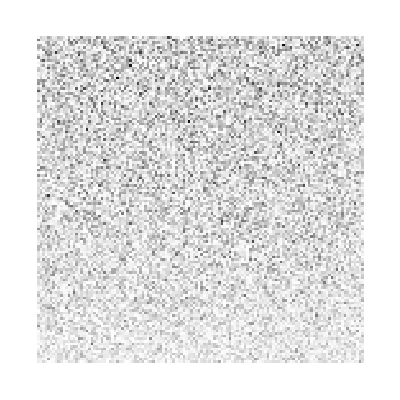
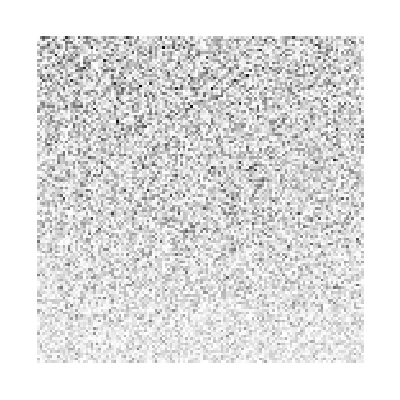
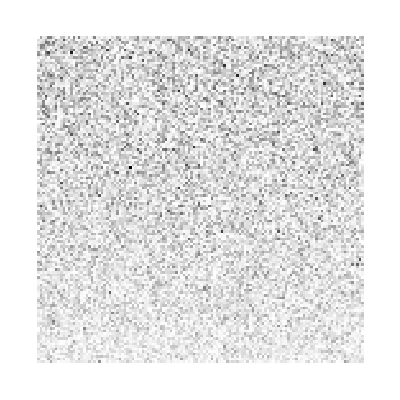
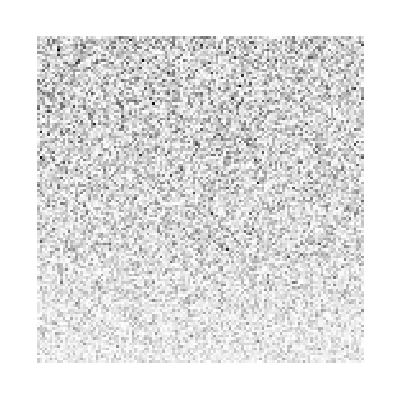
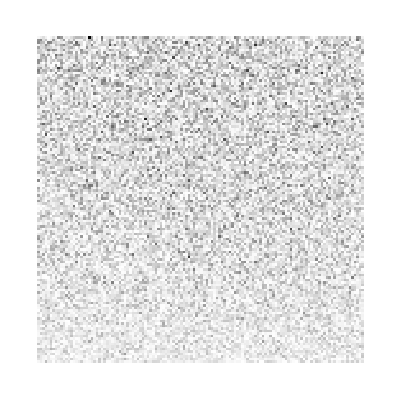
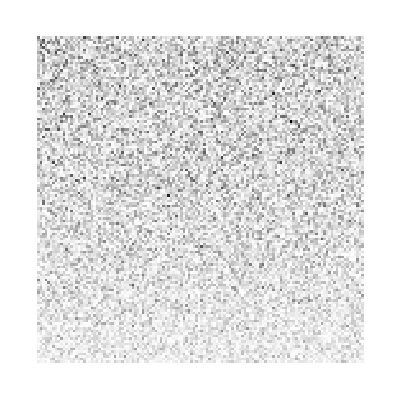

```mathematica
Map[ArrayPlot, Transpose[arrayList][[2]]]
```